# https://wolfr.am/ss2017training

# Training 4 programmers

## Working with symbols

With / Module / Block

```mathematica
With[
	{a = Map[Sqrt, {1, 2, 3}]}, 
	{a, a * 2}
]
```

```mathematica
Module[
	{temp = 4},
	(Print[temp];temp = Sqrt[temp]; temp ++; temp)
]
```

4

3

```mathematica
With[{a =2}, Hold[a+2]]
```

Hold[2+2]

```mathematica
Function[a, Hold[a+2]][2]
```

Hold[2+2]

```mathematica
Module[{a = 2}, Hold[a+2]]
```

Hold[a$3900+2]

```mathematica
$DateStringFormat
```

{DateTimeShort}

```mathematica
DateString[]
```

Wed 21 Jun 2017 14:09:23

```mathematica
Block[
	{Times = Plus},
	2*3
]
```

5

Set / SetDelayed

```mathematica
x = Map[f, {Print[1]; 1, 2, 3}]
```

```mathematica
x := Map[f, {Print[1]; 1, 2, 3}]
```

Rule / RuleDelayed

```mathematica
data = {"a" -> 2, "b" :> (Print[2];2), "c" :> 3 + 4}
```

```mathematica
Keys[data]
```

```mathematica
Values[data]
```

Clear your symbols!

```mathematica
ClearAll["Global`*"]
```

## Evaluation control

```mathematica
If[a == 2, 2+2, 3+3]
```

If[a==2,2+2,3+3]

```mathematica
Hold[3+4]
```

Hold[3+4]

```mathematica
Replace[Hold[3 + 4], Hold[x_ + y_] :> x * y]
```

```mathematica
SetAttributes[if, HoldRest]
if[True, true_, ___] := true
if[False, _, false_] := false

if[a == 2, Evaluate[3+4], 3+3]
```

if[a==2,7,3+3]

```mathematica
Attributes[And]
```

{Flat,HoldAll,OneIdentity,Protected}

```mathematica
Attributes[If]
```

{HoldRest,Protected}

```mathematica
Attributes[Table]
```

{HoldAll,Protected}

```mathematica
ClearAll[f]
SetAttributes[f, {HoldFirst}]
f[Plus[x_, y_]] := Times[x, y]
f[x_] := x;
```

```mathematica
f[3+4]
```

```mathematica
f[Evaluate[3+4]]
```

```mathematica
Length[Unevaluated[5+6+7+8]]
```

## Data structures

everything is data

```mathematica
{1,2, 3:>1} // FullForm
```

List[1,2,RuleDelayed[3,1]]

```mathematica
Map[f, Hold[1, 2, 3]]
```

Hold[f[1],f[2],f[3]]

```mathematica
Replace[{1,2, 3},x_ :> x + 2, {1}]
```

{3,4,5}

```mathematica
Replace[Hold[1,2, 3],x_ :> x + 2, {1}]
```

Hold[1+2,2+2,3+2]

data structures can be symbolic

```mathematica
data = {person["riccardo", 33], person["carlo", 33], {person["giulio", 51], person["dorian", 12]}, house["bentley university","175 forest street"]};
```

```mathematica
Mean @ Cases[data, person[_, age_] :> age, Infinity]
```

129/4

associations

```mathematica
<|"a" -> 2, "b" -> 3|>[["a"]]
```

2

```mathematica
First @ <|"a" -> 2, "b" -> 3|>
```

2

```mathematica
{2, 3}[[1]]
```

2

```mathematica
First@{2, 3}
```

2

writing data on disk

```mathematica
Put[
ArrayPlot[{{1,0,0,0.3},{1,1,0,0.3},{1,0,1,0.7}}], "Desktop/image.m"
]
```

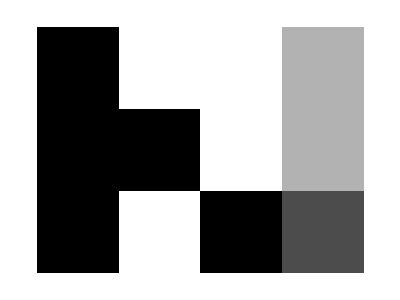

```mathematica
Get["Desktop/image.m"]
```

## Iterations

Procedural statements

```mathematica
While[True, PrintTemporary[RandomWord[]]]
```

```mathematica
Scan[Print,{a,b,c}]
```

```mathematica
Scan[If[# ≥3, Return[#]] &, {1, 2, 3, 4, 5}]
```

```mathematica
Scan[If[# ≥3, Return[#]] &, Hold[
Print["computed"]; 2+3,
Print["computed"]; 4+5, 
Print["computed"]; 6+7]
]
```

```mathematica
For[i=0,i<4,i++,Print[i]]
```

```mathematica
Do[Print[n^2],{n,4}]
```

Functional statements

```mathematica
Map[f, Hold[1+2, 3+4]]
```

```mathematica
MapAt[f,{{a,b,c},{d,e}},{All,2}]
```

{{a,f[b],c},{d,f[e]}}

```mathematica
Table[i^2,{i,10}]
```

```mathematica
MapIndexed[(Print[#2];#1 * First[#2]) &, {a, b, c}]
```

{1}

{2}

{3}

{a,2 b,3 c}

```mathematica
ParallelMap[f, Hold[1+2, 3+4]]
```

```mathematica
ParallelTable[i^2,{i,10}]
```

Replace: With + If

```mathematica
handleData[path_] := 
With[
{data = Import[path]},
If[
data =!= $Failed, 
Mean[data],
$Failed
]
]
```

```mathematica
handleData[path_] := 
Replace[
Import[path], {
$Failed -> $Failed,
any_:> Mean[any]
}
]
```

RuleDelayed in Replace

```mathematica
x:> 1+1
```

2:>1+1

```mathematica
RuleDelayed // Attributes
```

{HoldRest,Protected,SequenceHold}

```mathematica
Replace[{1, 2, 3}, {x_ :> x + 2}, {1}]
```

{3,4,5}

```mathematica
x = 2;
Replace[{1, 2, 3}, {x_ -> 4}, {1}]
```

{4,4,4}

Replace to iterate

```mathematica
Replace[{1,3,2,x,6,Pi}, _Integer ->"prime", {2}]
```

{1,3,2,2,6,π}

## Filters

```mathematica
Select[{1,2,4,7,6,2},EvenQ]
```

{2,4,6,2}

```mathematica
Cases[{1,2,4,7,6,2}, {___Integer?EvenQ}]
```

{2,4,6,2}

```mathematica
Cases[{1,2 -> 4,4,7,6,2}, HoldPattern[2-> x_] :> x]
```

{4}

```mathematica
Cases[{1,2 -> 4,4,7,6,2}, Verbatim[Rule][2, x_] :> x]
```

{4}

```mathematica
Reap[Sow[a];b;Sow[c];Sow[d];e]
```

{e,{{a,c,d}}}

## Pure functions

```mathematica
&
```

```mathematica
Function[{#1}][1, 2, 3]
```

{1}

```mathematica
Function[{#2}][1, 2, 3]
```

{2}

```mathematica
Function[##][1, 2, 3]
```

Sequence[1,2,3]

```mathematica
Function[{##2}][1, 2, 3]
```

{2,3}

```mathematica
Function["Hello "<> #name][<|"name" -> "jack", "age" -> 2|>]
```

Hello jack

```mathematica
Function[{name, lastname}, name]["jack", "sparrow"]
```

jack

## Aggregations

```mathematica
Fold[f,initial,Hold[a,b,c,d]]
```

f[f[f[f[initial,a],b],c],d]

```mathematica
FoldList[Plus,0,{a,b,c,d}]
```

{0,a,a+b,a+b+c,a+b+c+d}

```mathematica
NestWhile[#/2&,123456,EvenQ]
```

1929

## Levels

```mathematica
data = {{1, 1, 1}, {{2, 2}, {2, 2}}}
```

{{1,1,1},{{2,2},{2,2}}}

```mathematica
Level[data, 0]
```

{}

```mathematica
Level[data, 3]
```

{1,1,1,{1,1,1},2,2,{2,2},2,2,{2,2},{{2,2},{2,2}}}

```mathematica
Level[data, {3}]
```

{2,2,2,2}

```mathematica
Map[F, data]
```

{F[{1,1,1}],F[{{2,2},{2,2}}]}

```mathematica
Map[F, data, 1]
```

{F[{1,1,1}],F[{{2,2},{2,2}}]}

```mathematica
Map[F, data, 2]
```

```mathematica
Map[F, data, {2}]
```

```mathematica
Map[F, data, {3}]
```

{{1,1,1},{{F[2],F[2]},{F[2],F[2]}}}

```mathematica
Apply[f, data]
```

```mathematica
Apply[f,data, {1}]
```

```mathematica
Rule @ {1, 2}
```

```mathematica
Rule @@ {1, 2}
```

```mathematica
Rule @@@ {{1, 2}, {3, 4}}
```

```mathematica
Replace[data, 1 -> Sequence[]]
```

```mathematica
Replace[data, 1 -> Sequence[], {2}]
```

```mathematica
Replace[data, 1 -> Sequence[], {3}]
```

```mathematica
ReplaceAll[data, 1 -> Sequence[]]
```

## Sequence

```mathematica
{Sequence[1, 2, 3]}
```

```mathematica
ReplaceAll[{a, b, c}, a -> Sequence[1, 2, 3]]
```

{1,2,3,b,c}

```mathematica
Map[
	If[# ==1, Sequence[#, a, b, c], #]&,
	{1,2,3}
]
```

If::argb: If called with 6 arguments; between 2 and 4 arguments are expected.

General::stop: Further output of If::argb will be suppressed during this calculation.

{If[True,1,a,b,c,1],If[False,2,a,b,c,2],If[False,3,a,b,c,3]}

```mathematica
x -> Sequence[1, 2, 3]
```

2→Sequence[1,2,3]

```mathematica
Attributes[Rule]
```

{Protected,SequenceHold}

```mathematica
ClearAll[f]
SetAttributes[f, SequenceHold]
```

```mathematica
f[Sequence[x___]] := {x}
f[x_] :=x
```

```mathematica
f[Sequence[1, 2, 3]]
```

# Live Examples

importing CSV file:

```mathematica
data = Import["https://raw.githubusercontent.com/riccardodivirgilio/starthere/master/students.csv"];
```

```mathematica
MapAt[Hyperlink, Rest[data], {All, 1}]
```

{{,Jassim Moideen, Riccardo Di Virgilio},{,Federico Dradi, Riccardo Di Virgilio},{,Lina Baquero, Riccardo Di Virgilio},{,Daniele Baschieri, Riccardo Di Virgilio},{,Tyson Jones, Riccardo Di Virgilio},{,Mirian Lima,Paul Abbott},{,Arun Sharma,Paul Abbott},{,Carlos Arango,Paul Abbott},{,Patrick Griffin,Paul Abbott},{,Himanshu Raj,Giulio Alessandrini},{,Jan Segert,Giulio Alessandrini},{,Harish Chetty,Giulio Alessandrini},{,Nae Eoun Lee,Giulio Alessandrini},{,Hikari Sorensen,Giulio Alessandrini}}

```mathematica
nameddata = With[{headers = First[data]}, Map[AssociationThread[headers -> #] &, Rest[data]]];
```

```mathematica
nameddata[[All, "Repo"]]
```

{https://github.com/lazycrazyowl/Wolfram-Summer-School-2017-Jassim-Moideen,https://github.com/drigoF/WSS-drigo,https://github.com/lbaquerofierro-/MathematicaWSS17,https://github.com/DangerBlack/WSS17-personal-project,https://github.com/TysonRayJones/WSS17,https://github.com/mirianlima/hello-world,https://github.com/aksharmaWagner/wss2017-sharma,https://github.com/caarango/topic_exploration,https://github.com/Pgrfn5/WSS2017_PJG_Proj,https://github.com/himanshuraj04/wss17,https://github.com/JanSegert/wss2017,https://github.com/roronoaharish/WSS-17,https://github.com/lne817/WSS-17,https://github.com/hixor/wss_17}

```mathematica
MapAt[Hyperlink, nameddata, {All, "Repo"}] // Dataset
```

Dataset[<>]

interacting with an API:

```mathematica
deck = URLExecute[
"http://deckofcardsapi.com/api/deck/new/shuffle/", 
{"deck_count"-> 1},
"RawJSON"
]
```

<|shuffled→True,remaining→52,deck_id→0k3vphtwo96t,success→True|>

```mathematica
response = URLExecute["https://deckofcardsapi.com/api/deck/" <> Lookup[deck, "deck_id"]<> "/draw/", {"count" -> 2}, "RawJSON" ]
```

<|remaining→48,cards→{<|code→QS,image→http://deckofcardsapi.com/static/img/QS.png,suit→SPADES,value→QUEEN,images→<|png→http://deckofcardsapi.com/static/img/QS.png,svg→http://deckofcardsapi.com/static/img/QS.svg|>|>,<|code→7S,image→http://deckofcardsapi.com/static/img/7S.png,suit→SPADES,value→7,images→<|png→http://deckofcardsapi.com/static/img/7S.png,svg→http://deckofcardsapi.com/static/img/7S.svg|>|>},deck_id→0k3vphtwo96t,success→True|>

```mathematica
Map[Import, response[["cards", All,"image"]]]
```

{-Graphics-,-Graphics-}